0.4

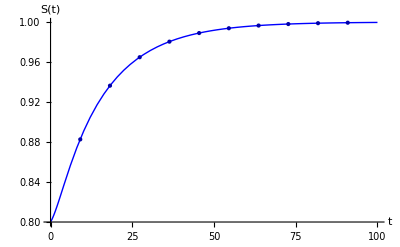

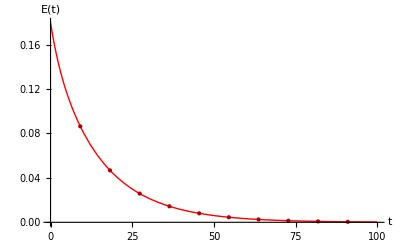

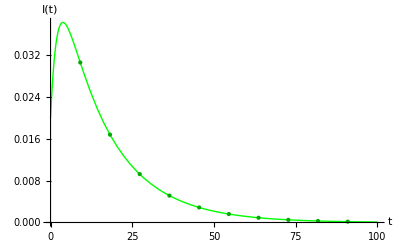

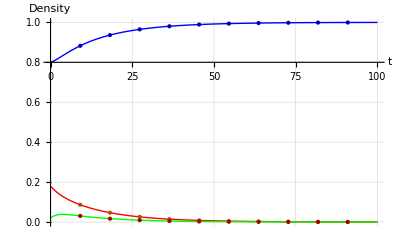

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n+γ i[t];
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t]-γ i[t];
n=1;
β=0.16;
ϵ=0.12;
γ=0.4;

R0=N[β/γ]

tf=100;
szero=0.80;
ezero=0.18;
izero=0.02;


sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

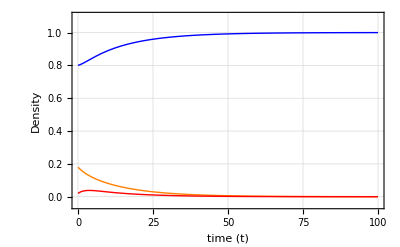

1.5

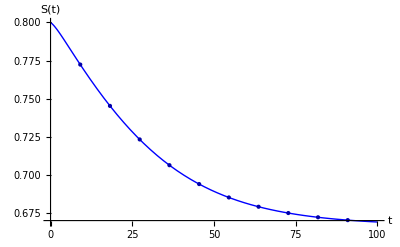

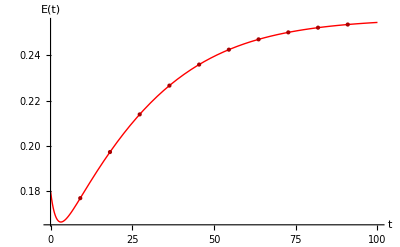

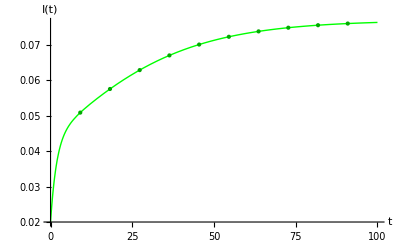

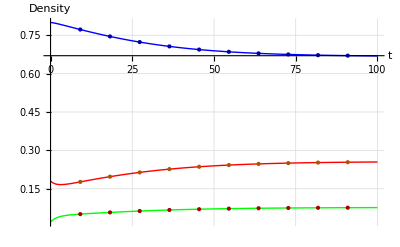

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n+γ i[t];
eq2=β*s[t]*i[t]/n-ϵ*e[t];
eq3=ϵ*e[t]-γ i[t];
n=1;
β=0.6;
ϵ=0.12;
γ=0.4;

R0=N[β/γ]

tf=100;
szero=0.80;
ezero=0.18;
izero=0.02;


sol=NDSolve[{s'[t]==eq1,e'[t]==eq2,i'[t]==eq3,s[0]==szero,e[0]==ezero,i[0]==izero},{s,e,i},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"E"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For E[t] versus t *)
plot2a=Plot[b[t]=Evaluate[e[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Orange,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For I[t] versus t *)
plot3a=Plot[c[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Orange,Line[{{0,0},{1,0}}]}],"E(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[e[t]/.sol],Evaluate[i[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","E(t)","I(t)"}, PlotStyle->{{Thick,Blue},{Thick,Orange},{Thick,Red}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

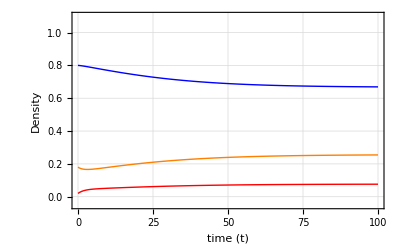

```mathematica
Clear["Global`*"]
J1={{(γ(γ-β))/(ϵ+γ),0},{-ϵ,-ϵ-γ}}
lam={{λ,0},{0,λ}}
Solve[λ(ϵ+γ)-γ(γ-β)==0,λ]
```

{{(γ (-β+γ))/(γ+ϵ),0},{-ϵ,-γ-ϵ}}

{{λ,0},{0,λ}}

{{λ→(γ (-β+γ))/(γ+ϵ)}}

0.4

{1,0,0}

{2.5,-1.15385,-0.346154}

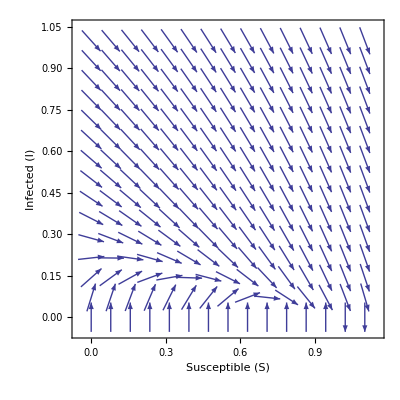

```mathematica
Clear["Global`*"]
β=0.16;
γ=0.4;
ϵ=0.12;
δ=1;
λ1=-(ϵ+γ+√((γ-ϵ)^2+4 β ϵ))/2;
λ2=-(ϵ+γ-√((γ-ϵ)^2+4 β ϵ))/2;
r0=β/γ
diff=β-γ;

e1={1,0,0}
e2={1/r0, γ/(ϵ+γ)(1-1/r0),ϵ/(ϵ+γ)(1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-β s i/1+γ i, ϵ(1-s-i)-γ i},{s,e1[[1]]-δ,e1[[1]]},{i,e1[[3]],e1[[3]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

1.5

{0.666667,0.25641,0.0769231}

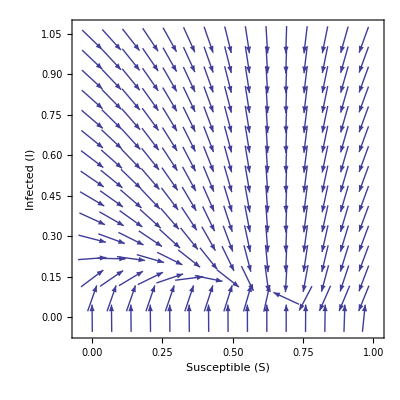

```mathematica
Clear["Global`*"]
β=0.6;
γ=0.4;
ϵ=0.12;
δ=0.5;
λ1=-(ϵ+γ+√((γ-ϵ)^2+4 β ϵ))/2;
λ2=-(ϵ+γ-√((γ-ϵ)^2+4 β ϵ))/2;
r0=β/γ
diff=β-γ;

e1={1,0,0};
e2={1/r0, γ/(ϵ+γ)(1-1/r0),ϵ/(ϵ+γ)(1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-β s i/1+γ i, ϵ(1-s-i)-γ i},{s,e2[[1]]-0.666667,e2[[1]]+0.3},{i,e2[[3]]-0.08,e2[[3]]+0.95},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

0.4

{1,0,0}

{2.5,-1.15385,-0.346154}

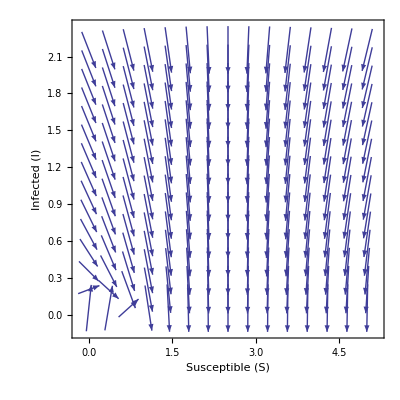

```mathematica
Clear["Global`*"]
β=0.16;
γ=0.4;
ϵ=0.12;
δ=2.5;

λ1=-γ-ϵ;
λ2=(γ(γ-β))/(γ+ϵ);
r0=β/γ


e1={1,0,0}
e2={1/r0, γ/(ϵ+γ)(1-1/r0),ϵ/(ϵ+γ)(1-1/r0)}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-β s i/1+γ i, ϵ(1-s-i)-γ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[3]]+0.4,e2[[3]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```